```mathematica
Directory[]
```

C:\Users\sxs\Documents\Matlab

```mathematica
SetDirectory["C:\\Users\\sxs\\Documents\\Matlab"]
```

C:\Users\sxs\Documents\Matlab

```mathematica
options=Import["Pride and Prejudice.txt","Elements"]
```

{Data,Lines,Plaintext,String,Words}

```mathematica
wordString=Import["Pride and Prejudice.txt","String"];
wordList=Import["Pride and Prejudice.txt","Words"];
wordListMMA = TextWords[wordString];
```

```mathematica
StringLength[wordString]
Length[wordList]
Length[wordListMMA]
```

717574

124588

124877

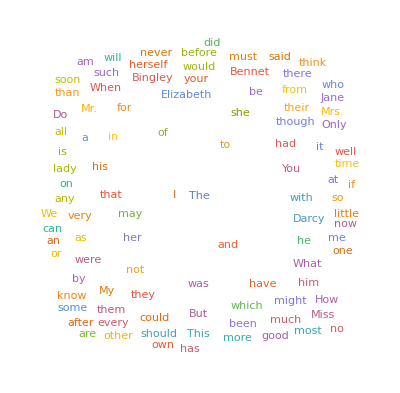

```mathematica
WordCloud[wordListMMA]
```

```mathematica
wordString=StringReplace[wordString,PunctuationCharacter:>" "];
wordString=StringDrop[wordString,{1,3}];
```

```mathematica
myWordList=StringSplit[wordString];
myWordList=DeleteStopwords[myWordList];
```

```mathematica
Length[myWordList]
```

49805

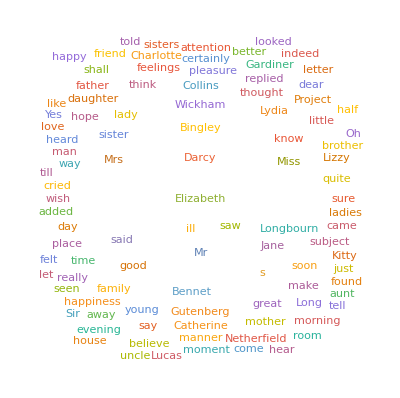

```mathematica
WordCloud[myWordList]
```

```mathematica
myWordCounts=WordCounts[StringJoin@Riffle[myWordList," "]];
wordCountsMMA=WordCounts[StringRiffle@myWordList];
wordCounts=Counts[myWordList];
```

```mathematica
Length/@{myWordCounts,wordCounts,wordCountsMMA}
```

{6722,6722,6722}